0.000351562

0.0015625

0.0075

0.0703125

0.24

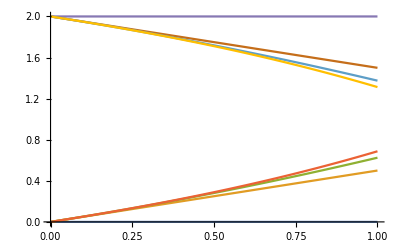

```mathematica
Ax=x[0]+x'[0] ϵ+x''[0] ϵ^2+Derivative[3][x][0] ϵ^3+O[ϵ]^4;
Bx=Normal[(Ax^2)-2Ax+ϵ==0];
Cx=Series[x[ϵ],{ϵ,0,3}];
Dx=Normal[Series[x[ϵ]^2-2x[ϵ]+ϵ==0,{ϵ,0,3}]];

(* Roots - O(1) Terms *)
Roots[x0(x0-2)==0,x0];x01=0;x02=2;
Roots[y0(-2+y0)==0,y0];y01=0;y02=2;

(* Roots - O(ϵ) Terms *)
Roots[1-2*x11+2*x01*x11==0,x11];
Roots[1-2*x12+2*x02*x12==0,x12];
x11=1/2;x12=-1/2;
Roots[1-2*y11+2*y01*y11==0,y11];
Roots[1-2*y12+2*y02*y12==0,y12];
y11=1/2;y12=-1/2;

(* Roots - O(ϵ^2) Terms *)
Roots[x11^2-2*x21+2*x01*x21==0,x21];
Roots[x12^2-2*x22+2*x02*x22==0,x22];
x21=1/8;x22=-1/8;
Roots[y11^2-y21+y01*y21==0,y21]
Roots[y12^2-y22+y02*y22==0,y22]
y21=1/4;y22=-1/4;

(* Roots - O(ϵ^3) Terms *)
Roots[2*x11*x21-2*x31+2*x01*x31==0,x31];
Roots[2*x12*x22-2*x32+2*x02*x32==0,x32];
x31=1/16;x32=-1/16;
Roots[y11*y21-(1/3)*y31+(1/3)*y01*y31==0,y31];
Roots[y12*y22-(1/3)*y32+(1/3)*y02*y32==0,y32];
y31=3/8;y32=-3/8;

(* Approximation of x Using all Order Roots up to O(ϵ^3) *)
xR1=x01+ϵ*x11+(ϵ^2)*x21+(ϵ^3)*x31;xR2=x02+ϵ*x12+(ϵ^2)*x22+(ϵ^3)*x32;
yR1=y01+ϵ*y11+(ϵ^2)*y21+(ϵ^3)*y31;yR2=y02+ϵ*y12+(ϵ^2)*y22+(ϵ^3)*y32;

(* Exact vs. Approx. Answer given ϵ = (0.05,0.1,0.2,0.5,0.8) Using First Root Only (To Simplfy Comparison) *)
xD1=Abs[(x01+0.05*x11+(0.05^2)*x21+(0.05^3)*x31)-(y01+0.05*y11+(0.05^2)*y21+(0.05^3)*y31)]
xD2=Abs[(x01+0.1*x11+(0.1^2)*x21+(0.1^3)*x31)-(y01+0.1*y11+(0.1^2)*y21+(0.1^3)*y31)]
xD3=Abs[(x01+0.2*x11+(0.2^2)*x21+(0.2^3)*x31)-(y01+0.2*y11+(0.2^2)*y21+(0.2^3)*y31)]
xD4=Abs[(x01+0.5*x11+(0.5^2)*x21+(0.5^3)*x31)-(y01+0.5*y11+(0.5^2)*y21+(0.5^3)*y31)]
xD5=Abs[(x01+0.8*x11+(0.8^2)*x21+(0.8^3)*x31)-(y01+0.8*y11+(0.8^2)*y21+(0.8^3)*y31)]

(* Plots of Approximation and Exact Solution *)
order11=0;order12=2;
order21=order11+(1/2)ϵ;order22=order12-(1/2)ϵ;
order31=order21+(1/8)(ϵ^2);order32=order22-(1/8)(ϵ^2);
order41=order31+(1/16)(ϵ^3);order42=order32-(1/16)(ϵ^3);

ordery11=0;ordery12=2;
ordery21=ordery11+(1/2)ϵ;ordery22=ordery12-(1/2)ϵ;
ordery31=ordery21+(1/4)(ϵ^2);ordery32=ordery22-(1/4)(ϵ^2);
ordery41=ordery31+(3/8)(ϵ^3);ordery42=ordery32-(3/8)(ϵ^3);

Plot[{order11,order21,order31,order41,order12,order22,order32,order42},{ϵ,0,1}]
Plot[{order41,order42,ordery41,ordery42},{ϵ,0,1},PlotLegends->"Expressions"]
```